```mathematica
readLog[path_]:=ToExpression/@(Import[path]//StringSplit[#,"\n"]&)
```

```mathematica
runningAvg[xs_,alpha_]:=
FoldList[
Function[
{old,new},
old*(1-alpha)+alpha*new
],
First[xs],
Drop[xs,1]
]
```

```mathematica
drawGroup[name_,d_,options_]:=Module[
{data=Map[Function[x,Drop[x,1]],d]},
ListPlot@@({
{{data[[All,1]],runningAvg[data[[All,2]],0.2]}ᵀ,
data},
PlotLabel->name,
Joined->True,
Filling->{2->{{1},Directive[RGBColor[0.990417, 0.500267, 0.0328679,0.3]]}},
PlotRange->All}~Join~options)]
```

```mathematica
drawVectorGroup[name_,d_,options_]:=Module[
{data=Last[d][[3]]},
ListPlot@@({
data,
PlotLabel->name,
Joined->True,
PlotRange->All}~Join~options)]
```

```mathematica
drawLogFile[path_]:=Module[{options,keys,data,groups},
data= readLog[path];
options=data[[1]];
keys=options[[All,1]];
options=Association[options];
data=Drop[data,1];
groups=GroupBy[data,#[[1]]&];
Row[
Table[
If[
ListQ[groups[k][[1,3]]],
drawVectorGroup[k,groups[k],options[k]],
drawGroup[k,groups[k],options[k]]
],
{k,keys}]
]]
```

```mathematica
stopAll[]:=Table[RemoveScheduledTask[t],{t,ScheduledTasks[]}]
```

```mathematica
Dynamic[display]
```

```mathematica
stopAll[];
SetDirectory[NotebookDirectory[]];
RunScheduledTask[
display=drawLogFile["../running-result/log.txt"];
Print["Redraw:"<> ToString[Now[]]],
{2,3000}];
```

Table::iterb: Iterator {t,Join[{},[]]} does not have appropriate bounds.

```mathematica
stopAll[]
```

Table::iterb: Iterator {t,Join[{},[]]} does not have appropriate bounds.

Table[RemoveScheduledTask[t],{t,Join[{},[]]}]

Table::iterb: Iterator {t,Join[{},[]]} does not have appropriate bounds.

Table[RemoveScheduledTask[t],{t,Join[{},[]]}]

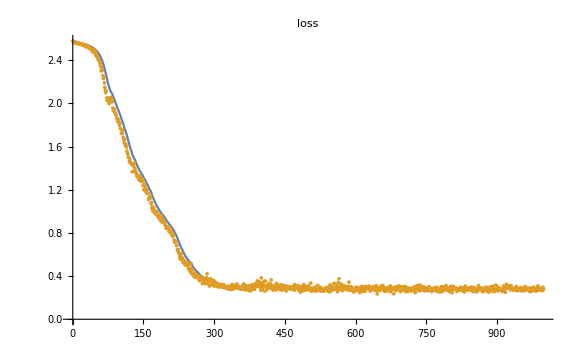
```mathematica
"Random vectors for new types and labels";
-Graphics-;
```